# Fixed Bandwidth Optimisation of F_(ψ,) θ_col, (β^*)_IP

## Constants + Cases

```mathematica
(*Normal Constants*)
sigT = 6.65*10^-29;
Me = 0.511*10^6;
eleccharge=1.6*10^-19;
```

```mathematica
(*Cases*)
DIANA1020 = {γ->1996, Elaser->1.17,ϵn->0.5*10^-6,ϕ->0,σL->25*10^-6,Q->100*10^-12,Epulse->100*10^-6,rep->100*10^6,tpulse->5.7*10^-12,σz->3*10^-3,EbSpread->10^-4,ELSpread->6.57*10^-4};
DIANA680 = {γ->1331,Elaser->1.17,ϵn->0.5*10^-6,ϕ->0,σL->25*10^-6,Q->100*10^-12,Epulse->100*10^-6,rep->100*10^6,tpulse->5.7*10^-12,σz->3*10^-3,EbSpread->10^-4,ELSpread->6.57*10^-4};
DIANA340 = {γ->665,Elaser->1.17,ϵn->0.5*10^-6,ϕ->0,σL->25*10^-6,Q->100*10^-12,Epulse->100*10^-6,rep->100*10^6,tpulse->5.7*10^-12,σz->3*10^-3,EbSpread->10^-4,ELSpread->6.57*10^-4};

Illya = {γ->665, Elaser->1.207,ϵn->0.5*10^-6,ϕ->0,σL->50*10^-6,Q->100*10^-12,Epulse->0.1,rep->100*10^6,tpulse->5.7*10^-12,σz->1*10^-3,EbSpread->1.9*10^-3, ELSpread->6.57*10^-4};

CBETA150 = {γ->293.54, Elaser->1.17,ϵn->0.3*10^-6,ϕ->0,σL->25*10^-6,Q->32*10^-12,Epulse->62*10^-6,rep->1.3*10^9,tpulse->10*10^-12,σz->1*10^-3,EbSpread->1.6*10^-3,ELSpread->6.57*10^-4};
CBETA114 = {γ->223.09,Elaser->1.17,ϵn->0.3*10^-6,ϕ->0,σL->25*10^-6,Q->32*10^-12,Epulse->62*10^-6,rep->1.3*10^9,tpulse->10*10^-12,σz->1*10^-3,EbSpread->1.6*10^-3,ELSpread->6.57*10^-4};
CBETA078 = {γ->152.64,Elaser->1.17,ϵn->0.3*10^-6,ϕ->0,σL->25*10^-6,Q->32*10^-12,Epulse->62*10^-6,rep->1.3*10^9,tpulse->10*10^-12,σz->1*10^-3,EbSpread->1.6*10^-3,ELSpread->6.57*10^-4};
```

```mathematica
(*Case Selection Variable*)
trialcase=CBETA150;
```

## Optimisation Parameters

```mathematica
(* Optimisation Parameters (BW + steps)*)
(*Bandwidth Limits*)
BWtop=10*1/100;
BWbot=1*1/100;
BWstep=0.05*1/100;
nBW=IntegerPart[(BWtop-BWbot)/BWstep];
(*Step Limits*)
θtop=20*10^-3;
θbottom = 0;
step=10^-6;
npoints=(θtop-θbottom)/step;
```

## Base Equations

```mathematica
(*Equations required for calculation of the constants*)
(*Recoil Parameter*)
Xrec[γ_,Einc_]:=(4*γ*Einc)/Me;
```

```mathematica
(*ψ from θ*)
ψ[θ_,γ_]:=γ*θ;
```

```mathematica
(*Compton Cross Section*)
σc[γ_,Einc_]:=sigT*(1-Xrec[γ,Einc]);
```

```mathematica
(*No. Electrons*)
Ne[Q_]:=Q/eleccharge;
```

```mathematica
(*No. Photons*)
NL[Epulse_,Einc_]:=Epulse/(Einc*eleccharge);
```

```mathematica
(*Constants for DIANA 1020 MeV Case*)
b[γ_,Einc_]:=Sqrt[12]*(1+Xrec[γ,Einc]);
c=Sqrt[12]/2;
d[γ_,ϵn_]:=2*γ*ϵn;
k[γ_,Einc_,Q_,Epulse_,f_]:=(σc[γ,Einc]*f*Ne[Q]*NL[Epulse,Einc])/(2*π);
(*f goes to z in derivation*)
z[σL_]:=σL^2;
g[ϵn_,γ_]:=ϵn/γ;
h[γ_,Einc_]:=CubeRoot[Xrec[γ,Einc]]/3;
j[γ_,Einc_]:=1+Xrec[γ,Einc]/2;
(*Energy Spread Terms*)
y[γ_,Einc_]:=1+Xrec[γ,Einc];
w[EbSpread_]:=EbSpread;
v[ELSpread_]=ELSpread;
```

## Calculation of Possible β - θ Space for Fixed Bandwidth and Requisite F_ψ

```mathematica
(*Array for Fcol, β and θ Values: {θ, β, Fcol}*)
Arr=Array[f,{nBW,4,npoints}];
```

```mathematica
(*Array for end of real solutions*)
Array[endpoint,{nBW}];
```

```mathematica
(*For Loop to get Fcol, β and θ Values*)
For[α=0,α<nBW,α++,
BW=BWbot+α*BWstep;
For[i=0,i<npoints,i++,
θ=i*step;
β=Sqrt[(d[γ,ϵn]/.trialcase)^2/(BW^2-((ψ[θ,γ]/.trialcase)^4/(((b[γ,Elaser]/.trialcase) +c*(ψ[θ,γ]/.trialcase)^2)^2))-((1+(y[γ,Elaser]/.trialcase))/((y[γ,Elaser]/.trialcase)+(ψ[θ,γ]/.trialcase)^2))^2*(w[EbSpread]/.trialcase)^2-((1+(ψ[θ,γ]/.trialcase)^2)/((y[γ,Elaser]/.trialcase)+(ψ[θ,γ]/.trialcase)^2))^2*(v[ELSpread]/.trialcase)^2)];

(*Break Condition to stop imaginary β*)
If[β==Re[β],
f[α+1,1,i+1]=θ;
f[α+1,2,i+1]=β;
f[α+1,3,i+1]=(k[γ,Elaser,Q,Epulse,rep]/.trialcase)/(f[α+1,2,i+1]*(g[ϵn,γ]/.trialcase)+(z[σL]/.trialcase))*((ψ[f[α+1,1,i+1],γ]/.trialcase)^2+(h[γ,Elaser]/.trialcase)*(ψ[f[α+1,1,i+1],γ]/.trialcase)^4)/(1+((j[γ,Elaser]/.trialcase)+1)*(ψ[f[α+1,1,i+1],γ]/.trialcase)^2+(j[γ,Elaser]/.trialcase)*(ψ[f[α+1,1,i+1],γ]/.trialcase)^4);
f[α+1,4,i+1]=BW;
endpoint[α+1]=i+1;
,
endpoint[α+1]=i;
Break[];
];
];
];
```

## β - θ Parameter Space Plots

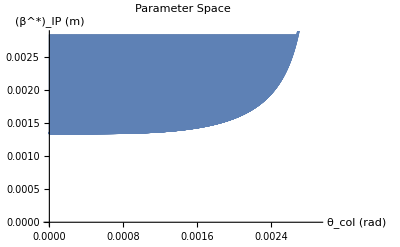

```mathematica
(*Plot β-θ Space for a single case*)
ListPlot[Transpose[{Arr[[nBW,1,All]],Arr[[nBW,2,All]]}],AxesLabel->{"θ_col (rad)","(β^*)_IP (m)"},PlotLabel->"Parameter Space",Filling->Top]
```

```mathematica
(*Plot β-θ Space for all cases*)
ListLinePlot[Table[Transpose[{Arr[[i,1,All]],Arr[[i,2,All]]}],{i,nBW}],AxesLabel->{"θ_col (rad)","(β^*)_IP (m)"},PlotLabel->"Parameter Space",PerformanceGoal->"Quality",PlotRange->{0,0.05},PlotLegends->Table[ToString[f[i,4,1]*100]<>"%",{i,nBW}]]
```

-Graphics-

## Finding F_ψ Maximised Values + Saving

```mathematica
(*Eta Array for Subscript[F, ψ] and BW maxes*)
Arr2=Array[η,{2,nBW}];
```

```mathematica
(*Zeta array for θ and β maxes*)
Arr3=Array[ζ,{2,nBW}];
```

```mathematica
(*Get BW Subscript[F^MAX, ψ] θ and β for this maximum*)
For[α=0,α<nBW,α++,
maxindex = Position[Arr⟦α+1⟧⟦3⟧,Max[Arr⟦α+1⟧⟦3⟧⟦1;;endpoint[α+1]⟧](*⟦1⟧*)]⟦1,1⟧;
(* BW, Flux, Angle, Beta*)
η[1,α+1]=f[α+1,4,maxindex];
η[2,α+1]=f[α+1,3,maxindex];
ζ[1,α+1]=f[α+1,1,maxindex];
ζ[2,α+1]=f[α+1,2,maxindex];
];
(*Function to tell when this is over*)
(*Get["GetNameFunction"];
SpeakName;*)
```

```mathematica
(*Saving the Arrays*)
SetDirectory[NotebookDirectory[]];
Arr2>>"CBETA150FBW1to10.txt"
Arr3>> "CBETA150BetaTheta1to10.txt"
```

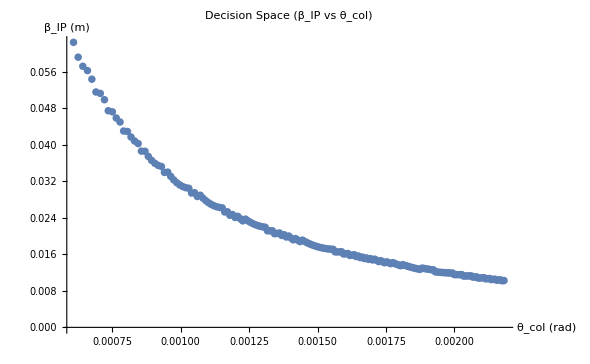

```mathematica
(*Maximum Points in the Parameter Space*)
ListPlot[ Transpose[Arr3],AxesLabel->{"θ_col (rad)","β_IP (m)"},PlotLabel->"Decision Space (β_IP vs θ_col)",PlotRange->All]
```

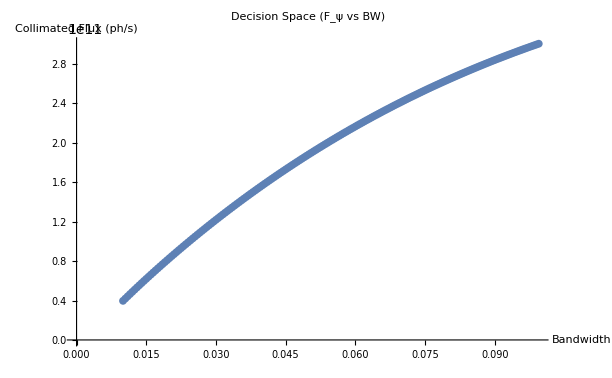

```mathematica
(*Plotting the Decision Space*)
ListPlot[ Transpose[Arr2],AxesLabel->{"Bandwidth","Collimated Flux (ph/s)"},PlotLabel->"Decision Space (F_ψ vs BW)"]
```

## Multiple Case Plots

```mathematica
(*Using multiple cases to create β-θ Maximum plots*)
SetDirectory[NotebookDirectory[]];
CBETAβθ150=<<"CBETA150BetaTheta1to10.txt";
CBETAβθ114=<<"CBETA114BetaTheta1to10.txt";
CBETAβθ078=<<"CBETA078BetaTheta1to10.txt";
```

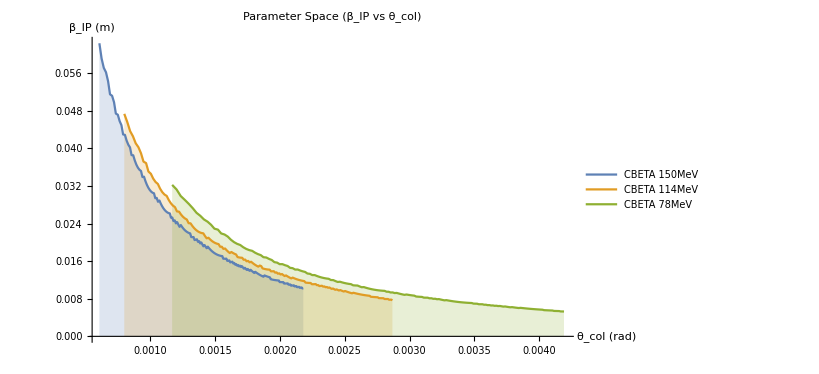

```mathematica
(*Plot*)
ListLinePlot[{Transpose[CBETAβθ150],Transpose[CBETAβθ114],Transpose[CBETAβθ078]},AxesLabel->{"θ_col (rad)","β_IP (m)"},PlotLabel->"Parameter Space (β_IP vs θ_col)",PlotLegends->Placed[{"CBETA 150MeV","CBETA 114MeV","CBETA 78MeV"},{0.7,0.7}],PlotRange->All,Filling->Axis]
```

```mathematica
(*Using Multiple Cases to create Subscript[F, ψ]-BW plots*)
SetDirectory[NotebookDirectory[]];
CBETAFBW150=<<"CBETA150FBW1to10.txt";
CBETAFBW114=<<"CBETA114FBW1to10.txt";
CBETAFBW078=<<"CBETA078FBW1to10.txt";
```

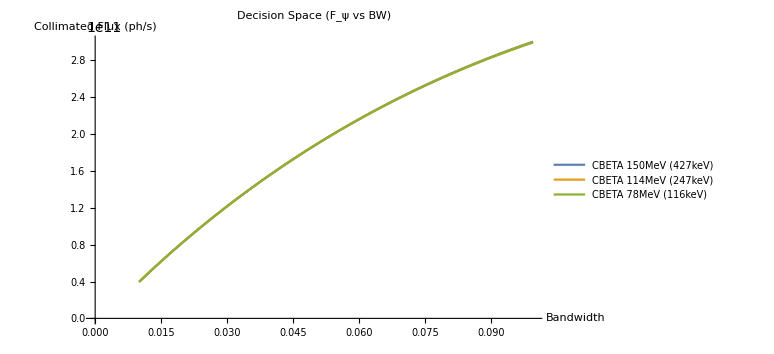

```mathematica
(*Plot*)
ListLinePlot[{Transpose[CBETAFBW150],Transpose[CBETAFBW114],Transpose[CBETAFBW078]},AxesLabel->{"Bandwidth","Collimated Flux (ph/s)"},PlotLabel->"Decision Space (F_ψ vs BW)",PlotLegends->Placed[{"CBETA 150MeV (427keV)","CBETA 114MeV (247keV)","CBETA 78MeV (116keV)"},{0.8,0.3}]]
```

## F_ψ Maximised Values (β-θ) for a Given Bandwidth (Single Case)

```mathematica
(*Trial Bandwidth*)
bw=0.5*1/100;
```

```mathematica
(*Storage Array*)
Arrsing=Array[υ,{3,npoints}];
```

```mathematica
For[i=0,i<npoints,i++,
θ=i*step;
β=Sqrt[(d[γ,ϵn]/.trialcase)^2/(bw^2-((ψ[θ,γ]/.trialcase)^4/(((b[γ,Elaser]/.trialcase) +c*(ψ[θ,γ]/.trialcase)^2)^2))-((1+(y[γ,Elaser]/.trialcase))/((y[γ,Elaser]/.trialcase)+(ψ[θ,γ]/.trialcase)^2))^2*(w[EbSpread]/.trialcase)^2-((1+(ψ[θ,γ]/.trialcase)^2)/((y[γ,Elaser]/.trialcase)+(ψ[θ,γ]/.trialcase)^2))^2*(v[ELSpread]/.trialcase)^2)];

(*Break Condition to stop imaginary β*)
If[β==Re[β],
υ[1,i+1]=θ;
υ[2,i+1]=β;
υ[3,i+1]=(k[γ,Elaser,Q,Epulse,rep]/.trialcase)/(υ[2,i+1]*(g[ϵn,γ]/.trialcase)+(z[σL]/.trialcase))*((ψ[υ[1,i+1],γ]/.trialcase)^2+(h[γ,Elaser]/.trialcase)*(ψ[υ[1,i+1],γ]/.trialcase)^4)/(1+((j[γ,Elaser]/.trialcase)+1)*(ψ[υ[1,i+1],γ]/.trialcase)^2+(j[γ,Elaser]/.trialcase)*(ψ[υ[1,i+1],γ]/.trialcase)^4);
υend=i+1;,
υend=i;
Break[];
];
];
```

```mathematica
(*Calculation of maximum Values*)
maxsingindex = Position[Arrsing⟦3⟧,Max[Arrsing⟦3⟧⟦1;;υend⟧]]⟦1,1⟧;

Fψ = Max[Arrsing⟦3⟧⟦1;;υend⟧];
βmax = υ[2,maxsingindex];
θmax = υ[1,maxsingindex];

Print[Fψ];
Print[βmax];
Print[θmax];
```

1.46374×10^10

0.122606

379/1000000